## Panel Plot Varying Delta and Kappa

### Set up data

```mathematica
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/export_data"];
```

```mathematica
dataDelta={Import["series_data/sim_delta_0.dat"],
Import["series_data/sim_delta_0p5.dat"],
Import["series_data/sim_delta_1.dat"],
Import["series_data/sim_delta_1p5.dat"],
Import["series_data/sim_delta_2.dat"],
Import["series_data/sim_delta_3.dat"]};

dataKappa={Import["series_data/sim_kappa_0p01.dat"],
Import["series_data/sim_kappa_0p02.dat"],
Import["series_data/sim_kappa_0p05.dat"],
Import["series_data/sim_kappa_0p1.dat"],
Import["series_data/sim_kappa_0p2.dat"],
Import["series_data/sim_kappa_100.dat"]};
```

```mathematica
(* baseline parameters are

x0=0.05; (* proportion of mitigators in 2010 *)
κ=0.05;
δ=1;
β=1;

(* temp prediction (linear extrapolation from previous temperatures) *) 
tempProjOnOff=1; (* on 1, off 0 *)
deltat=50; (* years looking ahead *)

*)
```

```mathematica
(* time ticks *)
timeTicks=Table[{50(i-1),1800+50(i-1)},{i,1,13}];

(* imgs size *)
imgs=325;
(* aspect ratio *)
aratio=0.6;
(* legend position (scaled) *)
legendPos={0.2,0.5};
(* labels (alphabet) *)
labels=Alphabet[];
(* label position (scaled) *)
labelPos={0.05,0.91};
(* bold label on off *)
bold=1;
```

```mathematica
{padLeft,padRight,padBottom,padTop}={50,30,40,20};  (* image padding *)
```

```mathematica
(* time plot range *)
plRange={100,400};
(* social plot range *)
plRangeSoc={-0.02,1.05};
(* emissions plot range *)
plRangeEm={-0.5,18.5};
(* temperature plot range *)
plRangeTemp={-0.1,5.3};
```

```mathematica
(* varying parameter values *)
deltaVals={0,0.5,1,1.5,2,3};
kappaVals={0.01,0.02,0.05,0.1,0.2,100};
```

```mathematica
(* type of f(T), variable (emissions,temp,cat,soc),  time step *)
dataDelta//Dimensions
```

{6,4,1201}

```mathematica
dataKappa//Dimensions
```

{6,4,1201}

```mathematica
(* plots to keep *)
plotNumsDelta={1,3,4,5};
plotNumsKappa={6,3,2,1};
```

```mathematica
tVals=Table[i,{i,0,1200}];
```

```mathematica
legendDelta=LineLegend[Table[TMBcolours[[i]],{i,Length[plotNumsDelta]}],Table["δ="<>ToString[deltaVals[[i]]],{i,plotNumsDelta}]]

legendKappa=LineLegend[Table[TMBcolours[[i]],{i,Length[plotNumsKappa]}],Table["κ="<>ToString[kappaVals[[i]]],{i,plotNumsKappa}]];
```

```mathematica
aratio
```

0.6

### Delta Plots

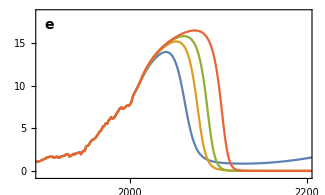

```mathematica
(* emissions plot delta *)
emissionPlotDelta=ListLinePlot[Table[Transpose[{tVals,dataDelta[[j,1]]}],{j,plotNumsDelta}],
PlotRange->{plRange,plRangeEm},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameLabel->{{None,None},{None,None}},
Epilog->Text[Style[labels[[5]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

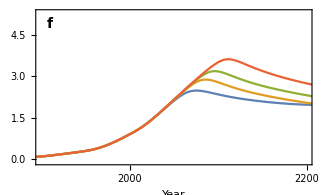

```mathematica
(* temp plot delta *)
tempPlotDelta=ListLinePlot[Table[Transpose[{tVals,dataDelta[[j,2]]}],{j,plotNumsDelta}],
PlotRange->{plRange,plRangeTemp},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
(*PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]]*)
FrameLabel->{{None,None},{"Year",None}},
Epilog->Text[Style[labels[[6]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

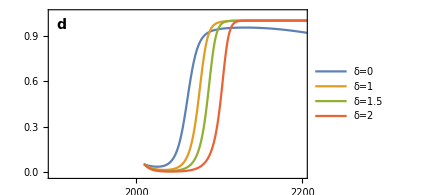

```mathematica
(* social plot delta *)
socPlotDelta=ListLinePlot[Table[Transpose[{tVals[[210;;]],dataDelta[[j,4,210;;]]}],{j,plotNumsDelta}],
PlotRange->{plRange,plRangeSoc},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
PlotLegends->Placed[legendDelta,Scaled[legendPos]],
FrameLabel->{{None,None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[4]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

### Kappa Plots

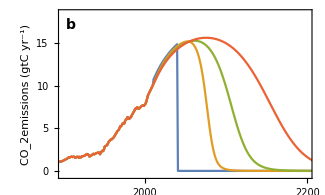

```mathematica
(* emissions plot delta *)
emissionPlotKappa=ListLinePlot[Table[Transpose[{tVals,dataKappa[[j,1]]}],{j,plotNumsKappa}],
PlotRange->{plRange,plRangeEm},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[2]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

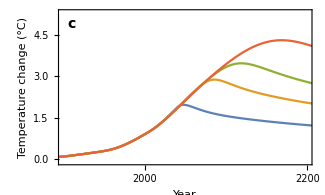

```mathematica
(* temp plot delta *)
tempPlotKappa=ListLinePlot[Table[Transpose[{tVals,dataKappa[[j,2]]}],{j,plotNumsKappa}],
PlotRange->{plRange,plRangeTemp},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
(*PlotLegends->Placed[legend=legend,Scaled[{0.8,0.5}]]*)
FrameLabel->{{"Temperature change (°C)",None},{"Year",None}},
Epilog->Text[Style[labels[[3]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

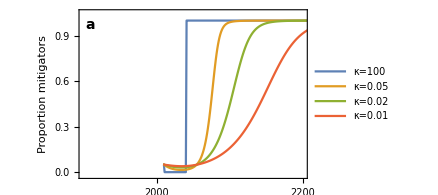

```mathematica
(* social plot delta *)
socPlotKappa=ListLinePlot[Table[Transpose[{tVals[[210;;]],dataKappa[[j,4,210;;]]}],{j,plotNumsKappa}],
PlotRange->{plRange,plRangeSoc},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
PlotLegends->Placed[legendKappa,Scaled[legendPos]],
FrameLabel->{{"Proportion mitigators",None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[1]],14,If[bold==1,Bold]],Scaled[labelPos]],
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

### Plot Grid

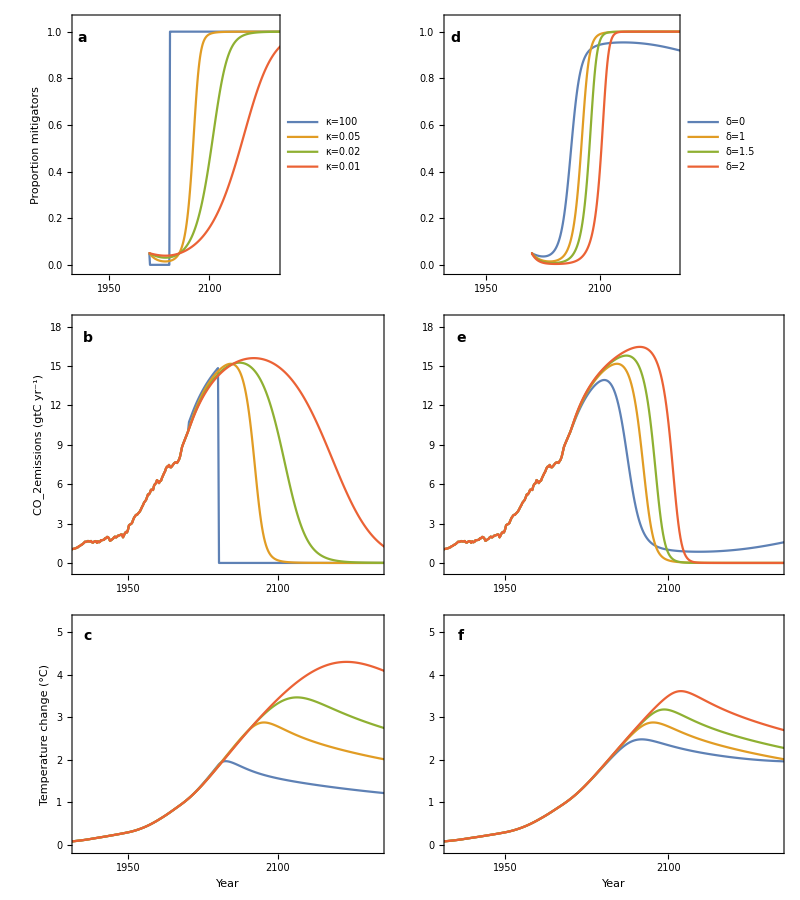

```mathematica
plotGrid=Grid[{{socPlotKappa,socPlotDelta},{emissionPlotKappa,emissionPlotDelta},{tempPlotKappa,tempPlotDelta}},Spacings->{-2.5,-2.2}]
```

```mathematica
Export["../figures/grid_kappa_delta.png",plotGrid,ImageResolution->100];
```